Model from the 2003 paper “EFFECTS OF FIRE AND HERBIVORY ON THE STABILITY OF SAVANNA ECOSYSTEMS”
Scenario C: high water influx, water_in=750

Define parameters:

```mathematica
u=0.6;
rh=1.0;
rw=0.5;
dh=0.9;dw=0.4;
alpha=0.4;
beta=300;
p=1;
win=807.8125; (*807.8125 for bifurcation*)
ws=alpha*(win-beta);
wt= win-ws;
```

Define system without fire effects:

```mathematica
hdot[H_,W_]:=rh*wt*(H)/(H+u*W+p*ws)-dh*H
wdot[H_,W_]:=rw*(wt*(u*W)/(H+u*W+p*ws)+ws)-dw*W
```

Find Nullclines and fixed points:

```mathematica
hnull=Simplify[Solve[hdot[H,W]==0,H]]
hnulleq=hnull[[All,1,2]];
hnull1=hnulleq[[1]]
hnull2=hnulleq[[2]];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{H→0.},{H→468.75-0.6 W}}

0.

```mathematica
wnull=Simplify[Solve[wdot[H,W]==0,H]]
wnulleq=wnull[[All,1,2]];
wnull1=wnulleq[[1]];
(*wnull2=wnulleq[[2]];*)
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{H→(51574.7+402.734 W-0.6 W^2)/(-253.906+1. W)}}

```mathematica
fp=Simplify[Solve[hdot[H,W]==0 && wdot[H,W]==0,{W,H}]]
fpnum=Transpose[{fp[[All,1]][[All,2]],fp[[All,2]][[All,2]]}];
fp1=fpnum[[1]]
fp2=fpnum[[2]]
fp3=fpnum[[3]]
(*fp4=fpnum[[4]]*)
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{W→-110.026,H→0.},{W→781.25,H→0.}}

{-110.026,0.}

{781.25,0.}

Part::partw: Part 3 of {{-110.026,0.},{781.25,0.}} does not exist.

{{-110.026,0.},{781.25,0.}}⟦3⟧

Plot things

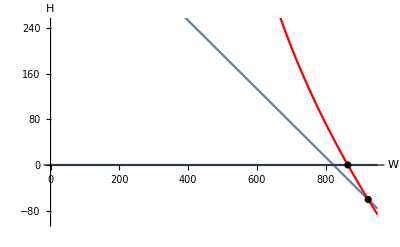

```mathematica
ph1=Plot[hnull1,{W,0,950},AxesLabel->{W,H}];
ph2=Plot[hnull2,{W,0,950}];
pw1=Plot[wnull1,{W,0,950},PlotStyle->Red];
(*pw2=Plot[wnull2,{W,0,750},PlotStyle->Red];*) 
points=ListPlot[{fp2,fp3},PlotStyle->Black];
Show[ph1,ph2,pw1,points,PlotRange->{-100,250}]
```

Stability Analysis

Unstable node fixed point: fp1 nonphysical

```mathematica
j11=D[hdot[H,W],H]/.fp[[1]];
j12=D[hdot[H,W],W]/.fp[[1]];
j21=D[wdot[H,W],H]/.fp[[1]];
j22=D[wdot[H,W],W]/.fp[[1]];
J={{j11,j12},{j21,j22}};
Eigenvectors[J];
Eigenvalues[J]
```

{3.31301,1.53631}

Stable node fixed point: fp2

```mathematica
j11=D[hdot[H,W],H]/.fp[[2]];
j12=D[hdot[H,W],W]/.fp[[2]];
j21=D[wdot[H,W],H]/.fp[[2]];
j22=D[wdot[H,W],W]/.fp[[2]];
J={{j11,j12},{j21,j22}};
Eigenvectors[J];
Eigenvalues[J]
```

{-0.317369,-0.0296809}

Unstable saddle fixed point : fp3

```mathematica
j11=D[hdot[H,W],H]/.fp[[3]];
j12=D[hdot[H,W],W]/.fp[[3]];
j21=D[wdot[H,W],H]/.fp[[3]];
j22=D[wdot[H,W],W]/.fp[[3]];
J={{j11,j12},{j21,j22}};
Eigenvectors[J];
Eigenvalues[J]
```

{-0.292641,0.032991}